## 4강 대수학

전경원 <ruddyscent@gmail.com>

2014년 9월 26일 금요일

## 다항식의 인수분해와 전개

다항식의 인수분해: 근

다항식의 전개: y축의 교점, 큰 수의 경향

```mathematica
Factor[-1+3x+x^2]
```

-1+3 x+x^2

#### 실습

f(x)=1+5x+2 x^3+10 x^4일 때,

Plot을 이용하여 f(x)의 실수 해를 추정해보자.

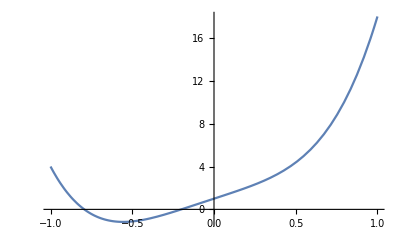

```mathematica
Plot[1+5x+2 x^3+10 x^4,{x,-1,1}]
```

Factor를 이용하여 f(x)의 실수 해를 찾아보자.

```mathematica
Factor[1+5x+2 x^3+10 x^4]
```

(1+5 x) (1+2 x^3)

```mathematica
Factor[1.+5x+2 x^3+10 x^4]
```

10. (0.2+1. x) (0.793701+1. x) (0.629961-0.793701 x+1. x^2)

## Solve와 NSolve로 다항식의 근 찾기

Solve와 N을 이용하여 다항식 x^3-15x+2의 근을 추정해보자.

```mathematica
Grid[Solve[x^3-15x+2==0,x],Alignment->Left]
%//N
%//Chop
```

x→5/(-1+2 ⅈ √31)^(1/3)+(-1+2 ⅈ √31)^(1/3)
x→-(5 (1+ⅈ √3))/(2 (-1+2 ⅈ √31)^(1/3))-1/2 (1-ⅈ √3) (-1+2 ⅈ √31)^(1/3)
x→-(5 (1-ⅈ √3))/(2 (-1+2 ⅈ √31)^(1/3))-1/2 (1+ⅈ √3) (-1+2 ⅈ √31)^(1/3)

x→3.80451-4.44089×10^-16 ⅈ
x→-3.938+0. ⅈ
x→0.133492+4.44089×10^-16 ⅈ

x→3.80451
x→-3.938
x→0.133492

위의 다항식의 해를 NSolve를 이용하여 구해보자.

```mathematica
Grid[NSolve[x^3-15x+2==0,x],Alignment->Left]
```

x→-3.938
x→0.133492
x→3.80451

## Reduce로 방정식과 부등식의 근 찾기

함수 f(x)=(x^3+5 x^2+4x+5)/(√(x^2+2x-3))의 정의역은 어떻게 될까?

```mathematica
Reduce[x^2+2x-3>0,x]
```

x<-3||x>1

양의 x가 증가할 때, 함수 f(x)를 분석해보자.

The square root of following polynomial is an symptotic curve of f(x):

```mathematica
PolynomialQuotient[(x^3+5 x^2+4x+5)^2,x^2+2x-3,x]
```

58+34 x+20 x^2+8 x^3+x^4

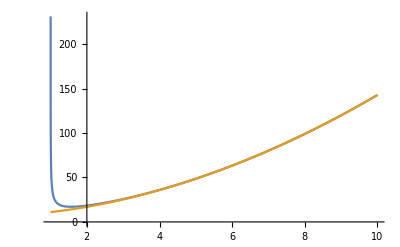

```mathematica
Plot[{(x^3+5 x^2+4x+5)/(√(x^2+2x-3)),√(x^4+8 x^3+20 x^2+34x+58)},{x,1,10}]
```

## 복소수 결괏값의 이해

매스매티카가는 -8의 삼중근 값으로 복소수를 반환한다.

```mathematica
(-8)^(1/3)//N
```

1.+1.73205 ⅈ

실수 계산의 결과로 복소수를 얻게 되는 경우가 종종있다.

```mathematica
Log[-2]
```

ⅈ π+Log[2]

```mathematica
ArcSin[2.]
```

1.5708-1.31696 ⅈ

```mathematica
Solve[x^2==-4,x]
```

{{x→-2 ⅈ},{x→2 ⅈ}}

```mathematica
Reduce[1+x+3 x^2+x^3==0,x,Cubics->True]
```

x==-1-(9-√57)^(1/3)/3^(2/3)-2/(3 (9-√57))^(1/3)||x==-1+((1+ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(3 (9-√57))^(1/3)||x==-1+((1-ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(3 (9-√57))^(1/3)

Reduce의 세 번째 매개변수로 Reals을 넣으면 실수해만 반환한다.

```mathematica
Reduce[ⅇ^x==-2,x,Reals]
```

False

```mathematica
Reduce[Sin[x]==2,x,Reals]
```

False

```mathematica
Reduce[x^2==-4,x,Reals]
```

False

```mathematica
Reduce[x^3==-8,x,Reals]
```

x==-2

```mathematica
Reduce[1+x+3 x^2+x^3==0,x,Reals,Cubics->True]
```

x==-1-(9-√57)^(1/3)/3^(2/3)-2/(3 (9-√57))^(1/3)

```mathematica
Reduce[x^3-15x+2==0,x,Reals,Cubics->True]//ToRadicals
%//ComplexExpand//Simplify
```

x==-(5 (1+ⅈ √3))/(2 (-1+2 ⅈ √31)^(1/3))-1/2 (1-ⅈ √3) (-1+2 ⅈ √31)^(1/3)||x==-(5 (1-ⅈ √3))/(2 (-1+2 ⅈ √31)^(1/3))-1/2 (1+ⅈ √3) (-1+2 ⅈ √31)^(1/3)||x==5/(-1+2 ⅈ √31)^(1/3)+(-1+2 ⅈ √31)^(1/3)

x==-2 √5 Cos[1/3 ArcTan[2 √31]]||x+√15 Sin[1/3 ArcTan[2 √31]]==√5 Cos[1/3 ArcTan[2 √31]]||x==√5 (Cos[1/3 ArcTan[2 √31]]+√3 Sin[1/3 ArcTan[2 √31]])

### 유리수 제곱근을 복소수로 정한 이유는?

매스매티카가 찾은 -8의 세제곱근은

```mathematica
ComplexExpand[(-8)^(1/3)]
```

1+ⅈ √3

사실, -8의 세제곱근은 하나가 아니다.

```mathematica
Reduce[x^3==-8,x]
```

x==-2||x==1-ⅈ √3||x==1+ⅈ √3

먼저, 제곱승을 하는 함수는 Power라는 것을 인지하자.

```mathematica
x^p//FullForm
```

Power[x,p]

음수에 양의 유리수 거듭제곱을 할 때, 지수의 분모가 홀수이면 실수를 반환하는 함수를 지수 함수를 생각해보자. 이 함수는 분자가 짝수이면 양, 홀수이면 음이 된다.

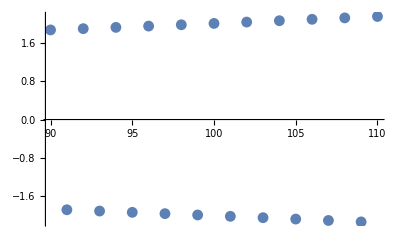

```mathematica
realPower[x_,p_]:=
If[x<0&&Element[p,Rationals],
If[OddQ[Denominator[p]],
If[OddQ[Numerator[p]],
-Power[-x,p],Power[-x,p]
],Power[x,p]
],Power[x,p]
]
Table[{x,realPower[-2,x/99]},{x,90,110}
]//ListPlot
realPower=.
```

이와는 달리 -8의 세제곱근 중, 제일 작은 편각을 갖는 주세제곱근을 -8의 세제곱근으로 정해보자.

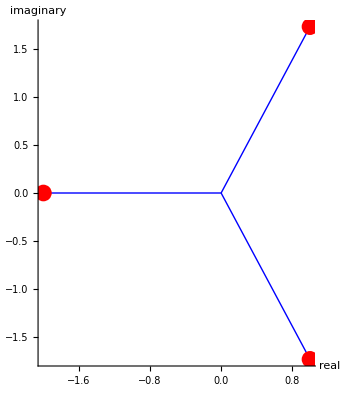

```mathematica
NSolve[x^3==-8,x];
Graphics[
{{Thick,Blue,Line[{{0,0},{Re[x],Im[x]}}]/.%},{Red,PointSize[.03],Point[{Re[x],Im[x]}]/.%}},
Axes->True,AxesLabel->{"real","imaginary"}
]
```

주제곱근을 사용하면 지수함수가 연속성을 갖게 된다.

```mathematica
N[{(-2)^(311/99),(-2)^(312/99)}]//Column
```

-7.96732-3.79246 ⅈ
-7.89809-4.07175 ⅈ

지수함수가 연속이 되면, 지수에 오는 유리수에 극한을 취해서 무리수 제곱값도 찾을 수 있다.

```mathematica
N[{(-2)^(311/99),(-2)^π,(-2)^(312/99)}]//Column
```

-7.96732-3.79246 ⅈ
-7.96618-3.7974 ⅈ
-7.89809-4.07175 ⅈ

복소수 함수의 연속성을 그래프로 확인해보자.

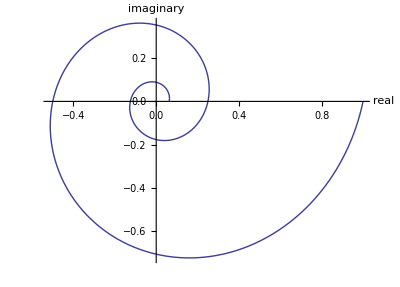

```mathematica
z=Table[(-2)^x,{x,-4,0,.01}];
ListLinePlot[Transpose@{Re[z],Im[z]},
AspectRatio->Automatic,Axes->True,AxesLabel->{"real","imaginary"}]
Clear[z];
```

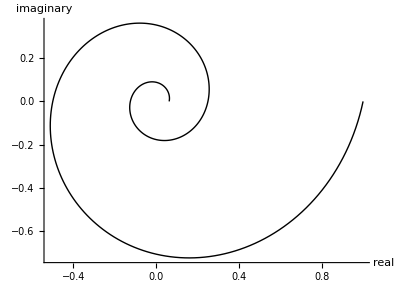

```mathematica
pwrs=Table[(-2)^x,{x,-4,0,.01}];
Graphics[Line[Table[{Re[z],Im[z]},{z,pwrs}]],Axes->True,AxesLabel->{"real","imaginary"}]
Clear[pwrs];
```

## 유리함수

### 방정식의 풀이

```mathematica
Solve[((x+3)(x-1))/(x-1)==0,x]
```

### 분수 식의 정리

```mathematica
Simplify[(1-x^5)/(1-x)]
```

```mathematica
Expand[(1-x)(1+x+x^2+x^3+x^4)]
```

팔레트를 이용하여 부분적으로 정리할 수도 있다.

```mathematica
(x^4+5 x^3+8 x^2+7x+3)/(3 x^4+14 x^3+18 x^2+10x+3)
```

### TraditionalForm의 이용

```mathematica
x-3
```

```mathematica
x-3//TraditionalForm
```

### 수직 점근선

분모의 해 중에서 분자의 해가 아닌 것은 그래프에서 수직 점근선으로 나타낸다.

```mathematica
k[x_]:=(x^4+3 x^3-x^2+5x-4)/(x^2-9)
```

```mathematica
Plot[k[x],{x,-10,10},Exclusions->{x^2-9==0},ExclusionsStyle->Directive[Gray,Dashed]]
```

### 다항식의 나눗셈

```mathematica
k[x_]:=(x^4+3 x^3-x^2+5x-4)/(x^2-9)
```

```mathematica
num=Numerator[k[x]]
```

```mathematica
den=Denominator[k[x]]
```

```mathematica
Expand[(8+3x+x^2)(x^2-9)+(68+32x)]==x^4+3 x^3-x^2+5x-4
```

```mathematica
Plot[{k[x],q[x]},{x,-15,15},Exclusions->{x^2-9==0},ExclusionsStyle->Directive[Gray,Dashed]]
```

### 부분분수 분해

```mathematica
Apart[(x^4+3 x^3-x^2+5x-4)/(x^2-9)]
```

```mathematica
Together[8+82/(3 (-3+x))+3 x+x^2+14/(3 (3+x))]
```

## 더욱 많은 표현

```mathematica
Simplify[Log[ⅇ^x]]
```

Log[ⅇ^x]

```mathematica
Simplify[Log[ⅇ^x],x∈Reals]
```

x

```mathematica
Simplify[√(x^2)]
```

√(x^2)

```mathematica
Simplify[√(x^2),x>0]
```

x

```mathematica
Simplify[√(x^2),x<0]
```

-x

#### 해의 검증

```mathematica
Clear[f,x];
f[x_]:=x^3-2x+9
```

```mathematica
Solve[f[x]==0,x]
realRoot=x/.%[[1]]
```

```mathematica
f[realRoot]
Simplify[%]
```

### 삼각함수

다음 삼각방정식을 증명해보자.
(sin(a t)+sin((2-a)t))/(2sin(t))=cos((1-a)t)

## 일반 방정식의 풀이

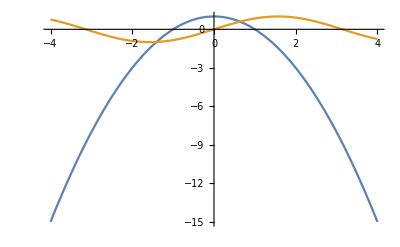

```mathematica
Plot[{1-x^2,Sin[x]},{x,-4,4}]
```

```mathematica
Solve[{1-x^2==Sin[x]},x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{1-x^2==Sin[x]},x]

```mathematica
NSolve[{1-x^2==Sin[x]},x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[{1-x^2==Sin[x]},x]

```mathematica
Reduce[{1-x^2==Sin[x]},x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{1-x^2==Sin[x]},x]

```mathematica
FindRoot[1-x^2-Sin[x],{x,{-1,1}}]
```

{x→{-1.40962,0.636733}}

## 점화식의 풀이

2014 람보르기니 우라칸 쿠페는 3억7,100만원입니다. 지금 돈이 한 푼도 없으므로, 연 8.9%의 이자로 5년 상환 대출을 받아 차를 사려고 합니다. 매달 정액 상환한다면 월 납입금은 얼마나 될까요?

```mathematica
s[n]==(1+0.089/12)s[n-1]-p
```

s[n]==-p+1.00742 s[-1+n]

```mathematica
Clear[s,p,n];
sols=RSolve[{s[n]==(1+0.089/12)s[n-1]-p[n],s[0]==371000000,s[60]==0,p[n]==p[n-1]},{s,p},n]
```

{{p→Function[{n},7.68336×10^6],s→Function[{n},-6.64958×10^8 (-1.55793+1. 1.00742^n)]}}

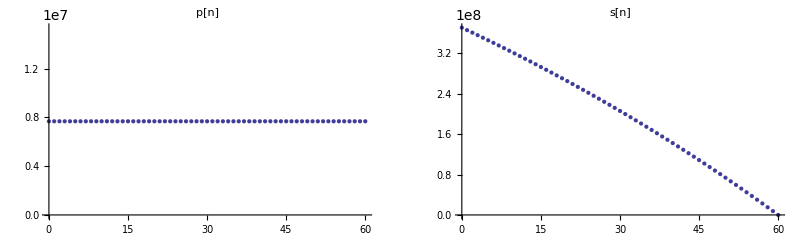

```mathematica
GraphicsRow[{ListPlot[Table[{n,p[n]/.sols⟦1⟧},{n,0,60}],PlotLabel->"p[n]"],ListPlot[Table[{n,s[n]/.sols⟦1⟧},{n,0,60}],PlotLabel->"s[n]"]}]
```

```mathematica
Grid[Prepend[Table[{n,s[n],(.089)/12 s[n-1],p[n]-(.089)/12 s[n-1],p[n]}/.sols⟦1⟧,
{n,1,60}
],
{"월","원리금 잔액","이자 지급분","원금 상환분","납입금"}
],
Dividers->Gray
]
```

월 | 원금 잔액 | 이자 지급분 | 원금 상환분 | 납입금
1 | 3.66068×10^8 | 2.75158×10^6 | 4.93177×10^6 | 7.68336×10^6
2 | 3.611×10^8 | 2.71501×10^6 | 4.96835×10^6 | 7.68336×10^6
3 | 3.56095×10^8 | 2.67816×10^6 | 5.0052×10^6 | 7.68336×10^6
4 | 3.51052×10^8 | 2.64104×10^6 | 5.04232×10^6 | 7.68336×10^6
5 | 3.45973×10^8 | 2.60364×10^6 | 5.07972×10^6 | 7.68336×10^6
6 | 3.40855×10^8 | 2.56596×10^6 | 5.11739×10^6 | 7.68336×10^6
7 | 3.357×10^8 | 2.52801×10^6 | 5.15535×10^6 | 7.68336×10^6
8 | 3.30506×10^8 | 2.48977×10^6 | 5.19358×10^6 | 7.68336×10^6
9 | 3.25274×10^8 | 2.45126×10^6 | 5.2321×10^6 | 7.68336×10^6
10 | 3.20003×10^8 | 2.41245×10^6 | 5.27091×10^6 | 7.68336×10^6
11 | 3.14693×10^8 | 2.37336×10^6 | 5.31×10^6 | 7.68336×10^6
12 | 3.09344×10^8 | 2.33398×10^6 | 5.34938×10^6 | 7.68336×10^6
13 | 3.03955×10^8 | 2.2943×10^6 | 5.38906×10^6 | 7.68336×10^6
14 | 2.98526×10^8 | 2.25433×10^6 | 5.42902×10^6 | 7.68336×10^6
15 | 2.93057×10^8 | 2.21407×10^6 | 5.46929×10^6 | 7.68336×10^6
16 | 2.87547×10^8 | 2.1735×10^6 | 5.50985×10^6 | 7.68336×10^6
17 | 2.81996×10^8 | 2.13264×10^6 | 5.55072×10^6 | 7.68336×10^6
18 | 2.76404×10^8 | 2.09147×10^6 | 5.59189×10^6 | 7.68336×10^6
19 | 2.70771×10^8 | 2.05×10^6 | 5.63336×10^6 | 7.68336×10^6
20 | 2.65096×10^8 | 2.00822×10^6 | 5.67514×10^6 | 7.68336×10^6
21 | 2.59378×10^8 | 1.96613×10^6 | 5.71723×10^6 | 7.68336×10^6
22 | 2.53619×10^8 | 1.92372×10^6 | 5.75963×10^6 | 7.68336×10^6
23 | 2.47816×10^8 | 1.88101×10^6 | 5.80235×10^6 | 7.68336×10^6
24 | 2.41971×10^8 | 1.83797×10^6 | 5.84538×10^6 | 7.68336×10^6
25 | 2.36082×10^8 | 1.79462×10^6 | 5.88874×10^6 | 7.68336×10^6
26 | 2.3015×10^8 | 1.75094×10^6 | 5.93241×10^6 | 7.68336×10^6
27 | 2.24173×10^8 | 1.70694×10^6 | 5.97641×10^6 | 7.68336×10^6
28 | 2.18153×10^8 | 1.66262×10^6 | 6.02074×10^6 | 7.68336×10^6
29 | 2.12087×10^8 | 1.61797×10^6 | 6.06539×10^6 | 7.68336×10^6
30 | 2.05977×10^8 | 1.57298×10^6 | 6.11038×10^6 | 7.68336×10^6
31 | 1.99821×10^8 | 1.52766×10^6 | 6.15569×10^6 | 7.68336×10^6
32 | 1.9362×10^8 | 1.48201×10^6 | 6.20135×10^6 | 7.68336×10^6
33 | 1.87373×10^8 | 1.43601×10^6 | 6.24734×10^6 | 7.68336×10^6
34 | 1.81079×10^8 | 1.38968×10^6 | 6.29368×10^6 | 7.68336×10^6
35 | 1.74739×10^8 | 1.343×10^6 | 6.34035×10^6 | 7.68336×10^6
36 | 1.68351×10^8 | 1.29598×10^6 | 6.38738×10^6 | 7.68336×10^6
37 | 1.61916×10^8 | 1.2486×10^6 | 6.43475×10^6 | 7.68336×10^6
38 | 1.55434×10^8 | 1.20088×10^6 | 6.48248×10^6 | 7.68336×10^6
39 | 1.48903×10^8 | 1.1528×10^6 | 6.53055×10^6 | 7.68336×10^6
40 | 1.42324×10^8 | 1.10437×10^6 | 6.57899×10^6 | 7.68336×10^6
41 | 1.35697×10^8 | 1.05557×10^6 | 6.62778×10^6 | 7.68336×10^6
42 | 1.2902×10^8 | 1.00642×10^6 | 6.67694×10^6 | 7.68336×10^6
43 | 1.22293×10^8 | 956896. | 6.72646×10^6 | 7.68336×10^6
44 | 1.15517×10^8 | 907008. | 6.77635×10^6 | 7.68336×10^6
45 | 1.0869×10^8 | 856750. | 6.82661×10^6 | 7.68336×10^6
46 | 1.01813×10^8 | 806119. | 6.87724×10^6 | 7.68336×10^6
47 | 9.48847×10^7 | 755113. | 6.92824×10^6 | 7.68336×10^6
48 | 8.79051×10^7 | 703729. | 6.97963×10^6 | 7.68336×10^6
49 | 8.08737×10^7 | 651963. | 7.03139×10^6 | 7.68336×10^6
50 | 7.37902×10^7 | 599813. | 7.08354×10^6 | 7.68336×10^6
51 | 6.66541×10^7 | 547277. | 7.13608×10^6 | 7.68336×10^6
52 | 5.94651×10^7 | 494351. | 7.18901×10^6 | 7.68336×10^6
53 | 5.22228×10^7 | 441033. | 7.24232×10^6 | 7.68336×10^6
54 | 4.49267×10^7 | 387319. | 7.29604×10^6 | 7.68336×10^6
55 | 3.75766×10^7 | 333207. | 7.35015×10^6 | 7.68336×10^6
56 | 3.01719×10^7 | 278693. | 7.40466×10^6 | 7.68336×10^6
57 | 2.27123×10^7 | 223775. | 7.45958×10^6 | 7.68336×10^6
58 | 1.51974×10^7 | 168450. | 7.51491×10^6 | 7.68336×10^6
59 | 7.62679×10^6 | 112714. | 7.57064×10^6 | 7.68336×10^6
60 | 0. | 56565.4 | 7.62679×10^6 | 7.68336×10^6